# Initialize

```mathematica
ReadQfile[fpath_]:=
Module[{s,table},
s=OpenRead[fpath];
table=ReadList[s,Number];
Close[s];
Return[table]
];
```

```mathematica
(* next step: Import data from station*)
ReadUSGSQfile[fpath_,headerrows_,ncolumns_,columnofinterest_,format_]:=
Module[{s,table,L},
s=OpenRead[fpath];
table=ReadList[s,String];
Close[s];
L=Length[table];

table=Table[0,{L-headerrows}];
s=OpenRead[fpath];
Skip[s,String,headerrows];

Do[
Skip[s,Word,columnofinterest-1];
table[[i]]=Read[s,format];
Skip[s,Word,ncolumns-columnofinterest];
,{i,L-headerrows}];
Close[s];

Return[table]
];
```

```mathematica
makemodelscatter[modelresults_,modelstn_,modelts_,timestart_,scalar_,offset_]:=
Module[{qtable,timetable,modelscatter},
qtable=Table[(modelresults[[modelstn]][[i]]*scalar+offset),{i,1,Length[modelresults[[modelstn]]]}];
timetable=Table[timestart+(i*modelts),{i,1,Length[modelresults[[modelstn]]]}];
modelscatter=Transpose[Table[{timetable,qtable}]];
Return[modelscatter]
];
(*model ts = the models' timestep, in units of the x-axis unit of the graph. E.g. with 10 minute output timestep for a fort.61, to show a graph in days requires "modelts" = 10 min / 60*24 (min/day) = 1/144. 5-minute would be 1/288.*)
```

```mathematica
scattercompare[modelscatter_,obscatter_]:=
Show[ListPlot[modelscatter,Joined->True],ListPlot[obscatter]];
```

# Load Model Results

```mathematica
wselist=Table[0,{9}];
scatterlist=Table[0,{9}];
(*Do[*)
filelist=
{
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\8652587_WSE_Timeseries_Spinup.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\8652587_WSE_Timeseries_Hurricane.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\8652587_WSE_Timeseries_Spindown.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\02083500_WSE_Timeseries_spinup.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\02083500_WSE_Timeseries_Hur.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\02083500_WSE_Timeseries_spindown.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\02084472_WSE_Timeseries_spinup.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\02084472_WSE_Timeseries_Hur.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\02084472_WSE_Timeseries_spindown.txt"
};

(*replaced; for irene the "spindown" fort.61 reflects the entire combined solution*)
Do[
fpath=filelist[[j]];
wselist[[j]]=ReadQfile[fpath];
(*,{i,1,Length[runlist]}];*)
,{j,1,Length[stationlist]}];

(*next step: timestamp each one in 10 minute intervals. date label scheme: days past run start date*)
startlist={0,45,55,0,45,55,0,45,55};
offsetlist={0,0,0,10,10,10,1,1,1};(*datum offset to convert ADCIRC results to common datum with gauge*)

Do[
scatterlist[[i]]=makemodelscatter[wselist,i,(1/288),startlist[[i]],3.28084,offsetlist[[i]]]
,{i,1,9}]
```

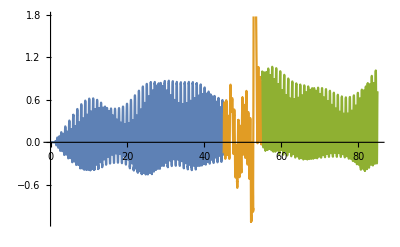

```mathematica
ListPlot[scatterlist[[1;;3]],Joined->True]
```

# Water Surface Elevations - 02084472

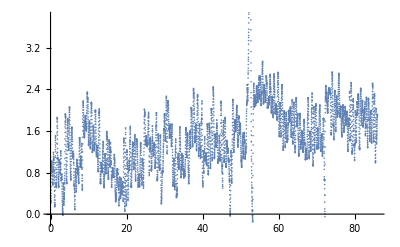

```mathematica
(*02084472*)
(*ReadUSGSQfile[fpath_,headerrows_,ncolumns_,columnofinterest_,format_]*)
Quiet[
fpath="C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\observed stage\\02084472.txt";
headerrows=26;
ncols=7;
datecol=3;
timecol=4;
stagecol=6;
stageseries=ReadUSGSQfile[fpath,headerrows,ncols,stagecol,Number];
dateseries=ReadUSGSQfile[fpath,headerrows,ncols,datecol,Word];
timeseries=ReadUSGSQfile[fpath,headerrows,ncols,timecol,Word];
abstimeseries=Table[AbsoluteTime[StringJoin[dateseries[[i]]," ",timeseries[[i]]]],{i,1,Length[timeseries]}];
stormstart=AbsoluteTime["2011,07,06"];
abstimeseriesdays=(abstimeseries-stormstart)/86400;
Obscatter02084472=Transpose[Table[{abstimeseriesdays,stageseries}]];
];

ScatterCompare[Obscatter02084472
```